```mathematica
DSolve[{x''[t]-2 x'[t]+x[t]==Sin[t],x[0]==0,x'[0]==1},x[t],t]
```

{{x[t]→1/2 (-ⅇ^t+3 ⅇ^t t+Cos[t])}}

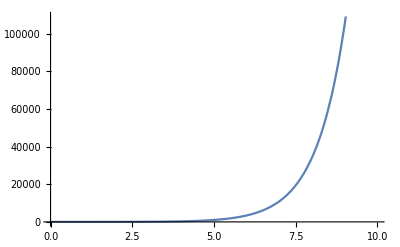

```mathematica
Plot[1/2 (-ⅇ^t+3 ⅇ^t t+Cos[t]),{t,0,10}]
```

```mathematica
p=NDSolve[{x''[t]-2 x'[t]+x[t]==Sin[t],x[0]==0,x'[0]==1},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

```mathematica
y=x[t]/.p(*转换*)
Plot[y,{t,0,10}]
```

{InterpolatingFunction[{{0., 10.}}, <>][t]}

-Graphics-